```mathematica
fileName = "/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json";
RadioButtonBar[
Dynamic[fileName],
{
"/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json",
"~/Downloads/optimizerHistory.json"
},Appearance->"Vertical"]
```

| /Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json
 | ~/Downloads/optimizerHistory.json

```mathematica
raw=Import[fileName];

raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

```mathematica
(*Optional: Drop rows with non-numeric values*)
(*Length[raw]
raw = Select[raw,AllTrue[Values[#],NumericQ]&];
Length[raw]*)
```

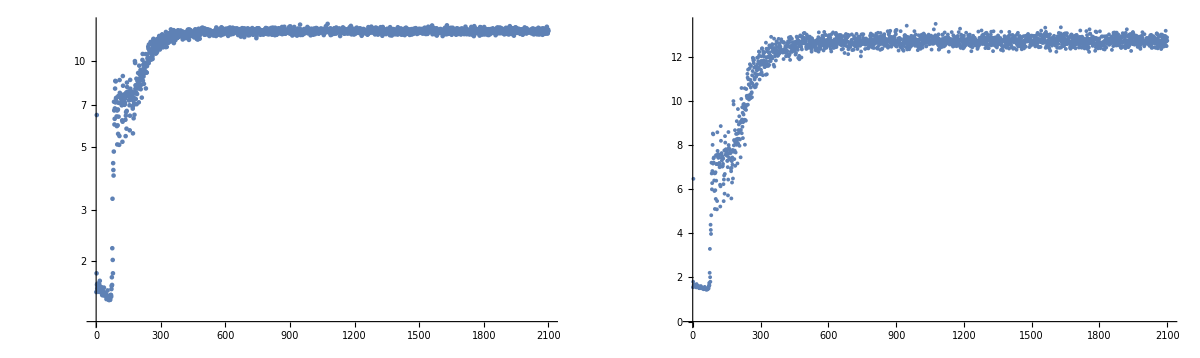

```mathematica
GraphicsGrid[{{
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->All,
Joined->False,
ImageSize->600
],
ListPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{0,All},
Joined->False,
ImageSize->600
]
}},ImageSize->1200]
```

### Live plot

```mathematica
(*Dynamic[livePlot]

makeLivePlot[]:=(
raw=Import[fileName];

raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];

livePlot = GraphicsGrid[{{
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->All,
Joined->False,
ImageSize->600
],
ListPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{0,All},
Joined->False,
ImageSize->600
]
}},ImageSize->1200];
)

task=CreateScheduledTask[makeLivePlot[],1]; (*Runs myFunction every 1 second*)
StartScheduledTask[task];*)
```

### Analyze

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]];
```

```mathematica
(*Format for yml*)
string = "";
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
];
string
```

L1PhaseSet : -14.6282135672
L2PhaseSet : -32.5049276217
S1ELkG : 1187.1751376001
S2ELkG : -3066.5983428703
S3ELkG : -1610.3388004667
S1EL_xOffset : 0.0007006943
S1EL_yOffset : -0.0001610188
S2EL_xOffset : -0.0003126498
S2EL_yOffset : -6.1141e-6
S2ER_xOffset : -0.0006682462
S2ER_yOffset : -0.0008713856
S1ER_xOffset : -0.0001284783
S1ER_yOffset : -0.0010995874
PDrive_median_x : -2.2173e-6
PDrive_median_y : 1.14e-6
PDrive_median_xp : -8.657e-7
PDrive_median_yp : 8.185e-7
PDrive_sigmaSI90_x : 0.0000315888
PDrive_sigmaSI90_y : 0.0000102052
PDrive_sigmaSI90_z : 0.0000348784
PDrive_sigmaSI90_xp : 0.0001177056
PDrive_sigmaSI90_yp : 0.0000281249
PDrive_emitSI90_x : 0.000046492
PDrive_emitSI90_y : 5.2019e-6
PDrive_norm_emit_x : 0.0000837724
PDrive_norm_emit_y : 6.7923e-6
PDrive_charge_nC : 1.6
PDrive_BMAG_x : 1.6955669018
PDrive_BMAG_y : 1.1490604737
PDrive_sliced_BMAG_x : List(1.5439546018,3.7440726325,1.4365574439,1.3220393134,1.0004766067)
PDrive_sliced_BMAG_y : List(1.83046721,1.2400052668,1.3928290733,1.2321858594,1.5188326046)
lostChargeFraction : 0.
errorTerm_lostChargeFraction : 0.
errorTerm_bunchSpacing : 0
errorTerm_transverseOffset : 0.
errorTerm_angleOffset : 0.
errorTerm_mainObjective : 0.5927756072
errorTerm_secondaryObjective : 1.9601e-6
maximizeMe : 13.4957873592
inputBeamFilePathSuffix : "/beams/2024-10-22_Impact_OneBunch/2024-10-22_oneBunch.h5"
csrTF : True

## Plot specific

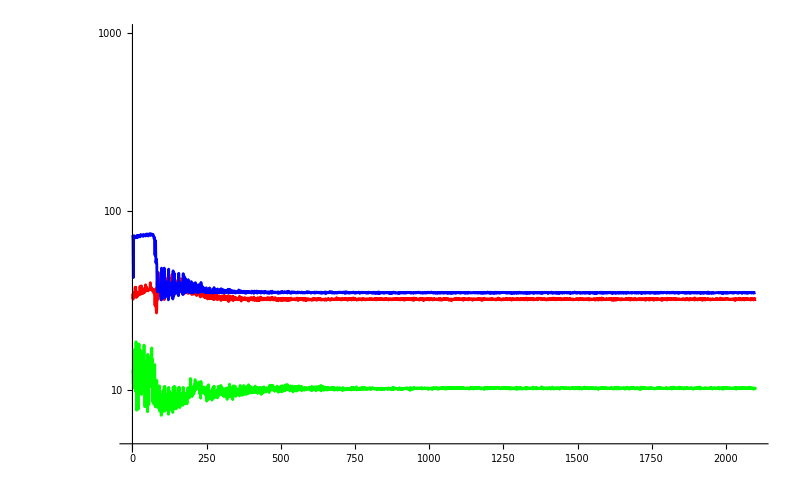

```mathematica
keys = {"PDrive_sigmaSI90_x","PDrive_sigmaSI90_y","PDrive_sigmaSI90_z","PWitness_sigmaSI90_x","PWitness_sigmaSI90_y","PWitness_sigmaSI90_z"};
ListLogPlot[
(10^6 raw[[All,#]]&/@keys)~Join~{(10^6 Max[#]&/@raw[[All,keys]])},
Joined->True,
ImageSize->800,
PlotStyle->{{Red},{Green},{Blue},{Red,Dashed},{Green,Dashed},{Blue,Dashed},{Black}},
InterpolationOrder->1,
PlotRange->{5,1000}
]
(*ListPlot[
raw[[All,#]]&/@{"PWitness_sigmaSI90_x","PWitness_sigmaSI90_y","PWitness_sigmaSI90_z"},
Joined->True
]*)
```

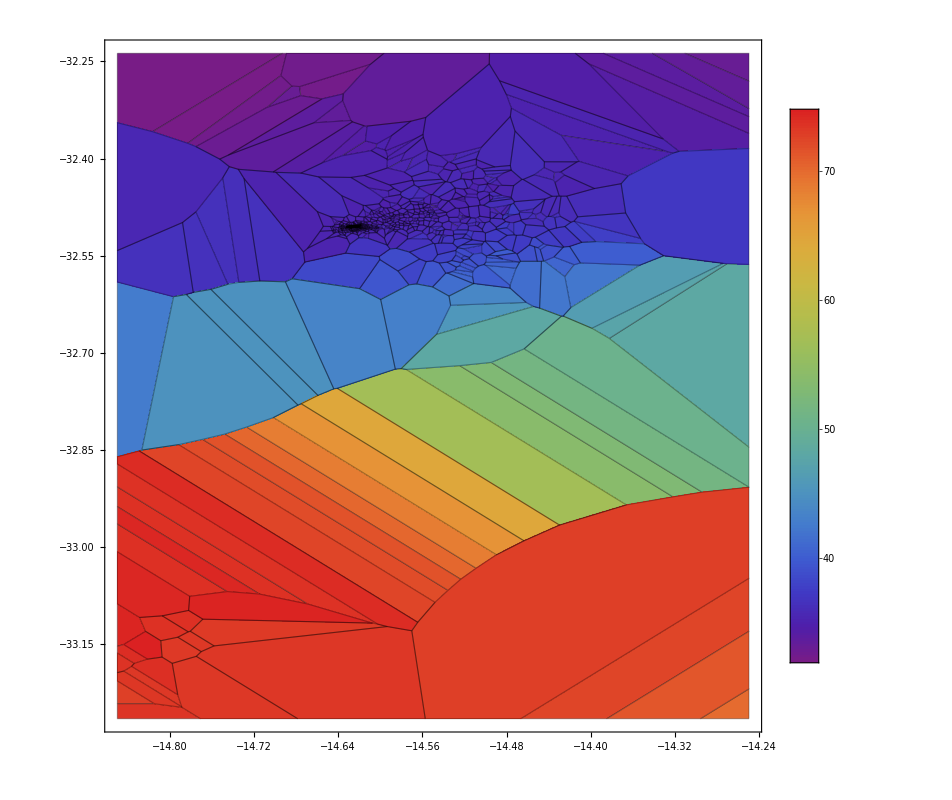

```mathematica
ListDensityPlot[{
#["L1PhaseSet"],
#["L2PhaseSet"],
10^6#["PDrive_sigmaSI90_z"]
(*10^6 Max[{#["PDrive_sigmaSI90_z"],#["PWitness_sigmaSI90_z"]}]*)
}&/@raw,ImageSize->800,
ColorFunction->"Rainbow",InterpolationOrder->0,PlotRange->All,Mesh->All,ColorFunction->"Rainbow",PlotLegends->Automatic]
```

## Plot all

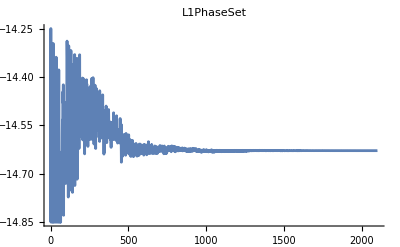
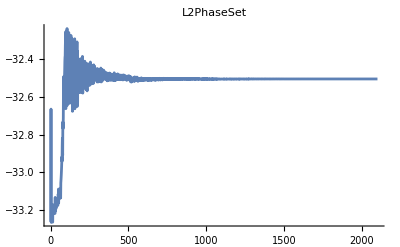
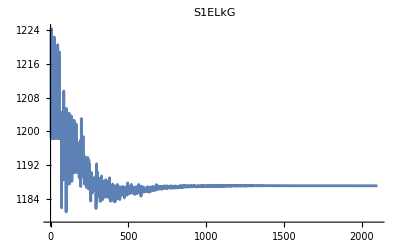
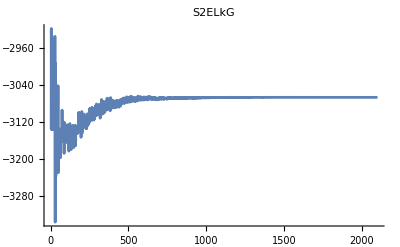
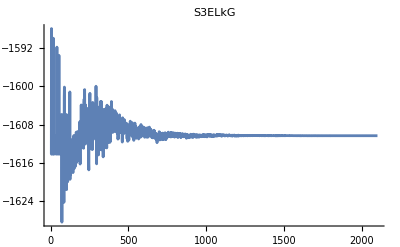
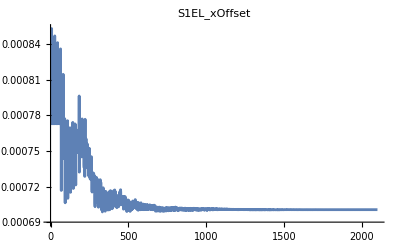
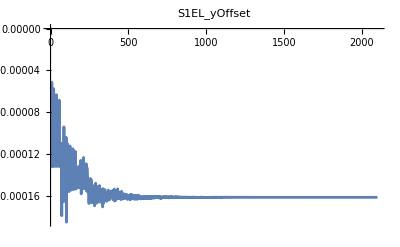
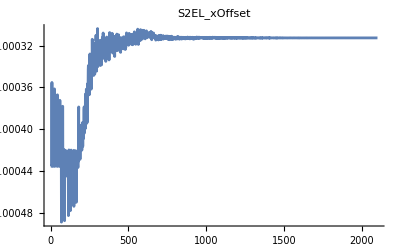
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | 0 | 0 | 0

```mathematica
imgArr=Table[
ListPlot[
raw[[All,key]],
PlotLabel->key,
ImageSize->400,
LabelStyle->15,
PlotRange->All,
Joined->True
],
{key,Keys[raw[[1]]]}
];

displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm
```

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
Export[
"~/srData.csv",
Dataset[raw]
]
```

~/srData.csv

## Linear model fit

```mathematica
freeVars=Intersection[
Keys[raw[[1]]],
{"QA10361kG","QA10371kG","QE10425kG","QE10441kG","QE10511kG","QE10525kG","L0BPhaseSet","L1PhaseSet","L2PhaseSet","L3PhaseSet","Q1EkG","Q2EkG","Q3EkG","Q4EkG","Q5EkG","Q6EkG","S1ELkG","S2ELkG","S3ELkG","S3ERkG","S2ERkG","S1ERkG","S1EL_xOffset","S1EL_yOffset","S2EL_xOffset","S2EL_yOffset","S2ER_xOffset","S2ER_yOffset","S1ER_xOffset","S1ER_yOffset","Q5FFkG","Q4FFkG","Q3FFkG","Q2FFkG","Q1FFkG","Q0FFkG", "XC1FFkG","XC3FFkG","YC1FFkG","YC2FFkG"}
]
(*Mathematica doesn't like underscores...*)
freeVarsMathematica=StringReplace[#,"_"->""]&/@freeVars;
```

{L1PhaseSet,L2PhaseSet,S1ELkG,S2ELkG,S3ELkG,XC1FFkG,XC3FFkG,YC1FFkG,YC2FFkG}

```mathematica
fitVar = "PDrive_twiss_beta_x"
(*fitVar = "bunchSpacing"*)
```

PDrive_twiss_beta_x

```mathematica
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
]
```

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

LinearModelFit[{{-29.7966,-41.4357,1329.27,-2921.16,-1423.08,0.,0.,0.,0.,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.1966,-41.4357,1329.27,-2921.16,-1423.08,0.,0.,0.,0.,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7966,-40.8357,1329.27,-2921.16,-1423.08,0.,0.,0.,0.,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7966,-41.4357,1355.17,-2921.16,-1423.08,0.,0.,0.,0.,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7966,-41.4357,1329.27,-2704.1,-1423.08,0.,0.,0.,0.,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7966,-41.4357,1329.27,-2921.16,-1396.83,0.,0.,0.,0.,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7966,-41.4357,1329.27,-2921.16,-1423.08,0.0148,0.,0.,0.,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7966,-41.4357,1329.27,-2921.16,-1423.08,0.,0.0074,0.,0.,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7966,-41.4357,1329.27,-2921.16,-1423.08,0.,0.,0.0074,0.,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7966,-41.4357,1329.27,-2921.16,-1423.08,0.,0.,0.,0.0076,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.6633,-41.3024,1335.03,-2872.92,-1417.25,-0.0148,0.00164444,0.00164444,0.00168889,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.6337,-41.2728,1336.3,-2862.2,-1415.95,-0.00328889,-0.00703457,0.00200988,0.0020642,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7717,-41.4108,1330.34,-2912.15,-1421.99,-0.000502469,0.00519472,0.000307065,0.000315364,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7911,-41.4302,1329.51,-2919.15,-1422.84,0.0146883,-0.000490063,0.0000682365,0.0000700808,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.6828,-41.3219,1334.18,-2879.98,-1418.1,-0.0102948,0.00131834,0.00140363,0.00144157,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.6629,-41.302,1335.04,-2872.78,-1417.23,-0.00178527,-0.00490175,0.0016493,0.00169387,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7551,-41.3942,1331.06,-2906.13,-1421.26,-0.000698453,0.0036522,0.000512128,0.000525969,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7679,-41.407,1330.51,-2910.75,-1421.82,0.0101396,-0.000506739,0.000354616,0.0003642,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.6958,-41.3349,1333.62,-2884.69,-1418.67,-0.00717291,0.00103951,0.00124337,0.00127697,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.6824,-41.3215,1334.2,-2879.84,-1418.08,-0.000895526,-0.0034212,0.00140862,0.00144669,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.744,-41.3831,1331.54,-2902.12,-1420.78,-0.000728561,0.00257154,0.000649092,0.000666635,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.6292,-41.2683,1336.5,-2860.59,-1415.76,-0.00175588,0.000802456,-0.00697945,0.0021208,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7152,-41.3543,1332.78,-2891.7,-1419.52,0.00662081,-0.00028973,-0.00265012,0.00103135,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.6988,-41.3379,1333.49,-2885.76,-1418.8,-0.00506553,0.00083643,0.00064853,0.00123945,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7973,-41.4364,1329.24,-2921.39,-1423.11,0.000468305,-0.0000451285,0.00726781,-8.3392×10^-6,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.6549,-41.294,1335.39,-2869.88,-1416.88,-0.00141608,0.000672964,-0.00480279,0.00179552,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.6627,-41.3018,1335.05,-2872.7,-1417.22,-0.000711796,-0.00223612,-0.00157226,0.00169669,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7316,-41.3707,1332.08,-2897.62,-1420.24,-0.000726,0.00183704,0.000309719,0.000824005,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7689,-41.408,1330.47,-2911.11,-1421.87,0.000129068,-0.0000788596,0.00501573,0.000351917,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.6723,-41.3114,1334.64,-2876.17,-1417.64,-0.00118001,0.000558102,-0.00330274,0.00157497,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7191,-41.3582,1332.62,-2893.09,-1419.69,0.00464197,-0.000304176,-0.00131365,0.000982547,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7019,-41.341,1333.36,-2886.88,-1418.94,-0.00358244,0.000662171,0.000348754,0.0012002,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.6797,-41.3188,1334.32,-2878.84,-1417.96,-0.000332323,-0.00156587,-0.000966159,0.00148159,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7237,-41.3628,1332.42,-2894.75,-1419.89,-0.000665855,0.00131715,0.000114793,0.000924469,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7504,-41.3895,1331.27,-2904.42,-1421.06,0.000235946,-0.000118253,0.00340575,0.000586071,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.6842,-41.3233,1334.12,-2880.49,-1418.16,-0.000963685,0.00045477,-0.00227783,0.00142389,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7169,-41.356,1332.71,-2892.29,-1419.59,0.00322032,-0.000268411,-0.000829428,0.00101055,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7042,-41.3433,1333.26,-2887.71,-1419.04,-0.00254313,0.000519998,0.000168754,0.00117122,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.6908,-41.3299,1333.84,-2882.85,-1418.45,-0.000113437,-0.00110054,-0.000583476,0.00134111,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7186,-41.3577,1332.64,-2892.94,-1419.67,-0.000581458,0.000947782,8.113×10^-6,0.000988122,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7378,-41.3769,1331.81,-2899.88,-1420.51,0.000269332,-0.000128597,0.00231713,0.000744858,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.6924,-41.3315,1333.77,-2883.45,-1418.52,-0.000775307,0.000365645,-0.00157582,0.00132014,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7153,-41.3544,1332.78,-2891.72,-1419.52,0.00224163,-0.000228126,-0.000517133,0.00103061,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7059,-41.345,1333.19,-2888.32,-1419.11,-0.00181213,0.000405702,0.0000639653,0.00114974,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.698,-41.3371,1333.53,-2885.47,-1418.77,6.4726×10^-6,-0.000776372,-0.000344081,0.00124963,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7155,-41.3546,1332.77,-2891.79,-1419.53,-0.000491635,0.00068437,-0.0000456944,0.00102808,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7293,-41.3684,1332.18,-2896.8,-1420.14,0.00026336,-0.000123407,0.00157988,0.000852703,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.6981,-41.3372,1333.53,-2885.49,-1418.77,-0.000616622,0.000290928,-0.0010937,0.00124873,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7141,-41.3532,1332.83,-2891.31,-1419.47,0.00156585,-0.000188969,-0.000317164,0.0010451,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7071,-41.3462,1333.13,-2888.78,-1419.17,-0.00129605,0.000314849,5.7372×10^-6,0.00113376,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7027,-41.3418,1333.33,-2887.16,-1418.97,0.0000665976,-0.000549752,-0.000196075,0.00119026,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7135,-41.3526,1332.86,-2891.09,-1419.44,-0.00040635,0.000495823,-0.0000686692,0.00105285,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7235,-41.3626,1332.43,-2894.71,-1419.88,0.000238312,-0.000110779,0.00107971,0.000926072,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7019,-41.341,1333.36,-2886.9,-1418.94,-0.000486007,0.000229556,-0.00076165,0.00119944,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7133,-41.3524,1332.87,-2891.01,-1419.44,0.00109775,-0.000153654,-0.000190253,0.00105564,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7081,-41.3472,1333.09,-2889.12,-1419.21,-0.000930328,0.000243272,-0.0000242057,0.00112182,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7057,-41.3448,1333.2,-2888.26,-1419.1,0.0000916083,-0.00039075,-0.000105965,0.00115187,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7123,-41.3514,1332.91,-2890.65,-1419.39,-0.000330273,0.000360374,-0.0000743673,0.00106798,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7196,-41.3587,1332.6,-2893.28,-1419.71,0.000205874,-0.0000954127,0.000739745,0.000976076,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7046,-41.3437,1333.24,-2887.87,-1419.06,-0.000380303,0.000179908,-0.00053227,0.00116531,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7127,-41.3518,1332.89,-2890.79,-1419.41,0.000772423,-0.00012321,-0.000110603,0.00106335,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7088,-41.3479,1333.06,-2889.37,-1419.24,-0.000670186,0.000187282,-0.0000374052,0.00111289,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7076,-41.3468,1333.11,-2888.96,-1419.19,0.0000968306,-0.000278777,-0.0000522273,0.00112718,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7084,-41.3475,1333.08,-2889.22,-1419.22,0.0000315787,-0.000181129,-0.0000556098,0.00111813,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.6037,-41.2428,1337.6,-2851.37,-1414.64,-0.000226425,0.0000413471,-0.000138952,-0.00684526,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7672,-41.4063,1330.54,-2910.49,-1421.79,-0.0000345926,6.3169×10^-6,-0.0000212288,0.00539309,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7096,-41.3487,1333.03,-2889.67,-1419.27,0.000230703,-0.000177137,0.000506883,0.000528935,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7054,-41.3445,1333.21,-2888.15,-1419.09,-0.000286955,0.00012536,-0.000373511,0.00106809,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-30.3307,-41.2364,1337.87,-2849.06,-1414.36,-0.000213368,0.0000306289,-0.00010839,0.0019316,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.9567,-41.2995,1335.15,-2871.88,-1417.12,0.000558333,-0.000191465,-0.0000867591,0.00100064,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-30.0123,-41.2893,1335.59,-2868.18,-1416.67,-0.0000263747,0.000174649,-0.0000754766,0.000969294,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7548,-41.3386,1333.46,-2886.01,-1418.83,0.0000227247,-0.000126774,-0.000058645,0.00109539,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7191,-41.3459,1333.15,-2888.66,-1419.15,-0.000672154,0.000199361,-0.0000380797,0.00110784,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.898,-41.2258,1338.33,-2845.19,-1413.89,-0.000220908,0.0000444777,-0.000107355,-0.00423688,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7871,-41.3787,1331.73,-2900.52,-1420.59,-0.0000630574,0.000012147,-0.0000343869,0.00392184,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.9612,-41.2934,1335.41,-2869.67,-1416.85,0.000552008,-0.000190169,-0.0000896831,0.000673702,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.9242,-41.3014,1335.07,-2872.57,-1417.21,0.000364983,-0.000130658,-0.0000817993,0.000740028,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-30.0235,-41.2852,1335.77,-2866.71,-1416.5,0.000311684,-0.000173061,0.000310573,0.000640549,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.754,-41.3354,1333.6,-2884.87,-1418.69,-0.000195496,0.0000797677,-0.000268998,0.00100277,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.2701,-41.4153,1330.15,-2913.76,-1422.19,0.000242069,-0.0000674104,9.7612×10^-6,-0.00042937,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-30.1686,-41.2638,1336.69,-2858.94,-1415.56,-0.000143787,0.0000156507,-0.0000903391,0.00157089,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.9379,-41.2965,1335.28,-2870.8,-1416.99,-0.0000310264,0.000121642,-0.0000470269,0.000512503,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7828,-41.3322,1333.74,-2883.68,-1418.55,0.0000145128,-0.0000888213,-0.00005687,0.00100634,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.9046,-41.2461,1337.46,-2852.55,-1414.78,0.0000719936,-0.0000397161,-0.0000762812,-0.00296183,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8051,-41.3584,1332.61,-2893.19,-1419.7,-0.0000424246,4.2235×10^-6,-0.0000407874,0.00287017,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7411,-41.336,1333.57,-2885.08,-1418.72,-0.000446582,0.000133062,-0.0000197551,0.000693344,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.9084,-41.3021,1335.04,-2872.82,-1417.24,0.0000581003,-0.0000655198,0.000222831,0.000361842,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7776,-41.3304,1333.82,-2883.03,-1418.47,-0.000156752,0.000057571,-0.000193858,0.000904849,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.9294,-41.3003,1335.12,-2872.16,-1417.16,0.000373593,-0.00013559,-0.0000651014,0.000718268,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7699,-41.3306,1333.81,-2883.11,-1418.48,-0.000321278,0.0000920182,-0.000026683,0.000697152,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.4133,-41.3874,1331.36,-2903.66,-1420.97,0.0000313557,-1.2082×10^-6,0.0000196284,-0.000353449,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.717,-41.3313,1333.78,-2883.36,-1418.51,-0.000123201,0.000122733,3.159×10^-6,-0.0000910688,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7727,-41.332,1333.75,-2883.63,-1418.54,-6.5269×10^-6,-0.0000565004,-0.0000476989,0.00083868,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-30.1664,-41.2637,1336.69,-2858.93,-1415.56,-0.000148463,0.0000228331,-0.0000883011,0.00153364,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.5283,-41.3685,1332.17,-2896.83,-1420.14,3.8834×10^-6,2.4648×10^-6,3.1392×10^-6,-0.0000651438,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7131,-41.2949,1335.35,-2870.22,-1416.92,-0.0000643917,0.0000170106,-0.0000181237,-0.00234227,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.791,-41.3487,1333.03,-2889.68,-1419.27,-0.0000457807,6.1771×10^-6,-0.0000373249,0.00207382,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7436,-41.3271,1333.96,-2881.85,-1418.33,0.0000745963,-0.0000477577,0.000169731,-0.00011718,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7724,-41.3299,1333.84,-2882.85,-1418.45,-0.000121407,0.0000414791,-0.000138309,0.000748706,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7518,-41.3267,1333.98,-2881.72,-1418.31,0.000283537,-0.0000934359,-0.000022249,0.000101974,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7671,-41.33,1333.84,-2882.89,-1418.45,-0.000228875,0.0000636849,-0.0000260056,0.000606222,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7185,-41.9314,1339.53,-2835.17,-1412.68,-0.0000886015,0.0000127346,-0.000054711,0.000933842,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-30.0291,-41.5237,1338.26,-2845.79,-1413.97,-0.000113037,0.0000125519,-0.0000707058,0.00122098,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.9079,-40.8702,1330.62,-2909.81,-1421.71,-0.0000259823,2.2416×10^-6,-0.00001641,0.000285806,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7474,-41.7693,1338.17,-2846.57,-1414.06,-0.0000790347,0.0000111315,-0.0000488594,0.000834836,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8257,-41.5463,1338.27,-2845.72,-1413.96,-0.0000761929,9.9×10^-6,-0.0000363593,-0.00112951,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8204,-41.5161,1337.47,-2852.44,-1414.77,-0.0000715466,9.3312×10^-6,-0.0000365068,-0.000640109,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8546,-41.604,1338.38,-2844.83,-1413.85,-0.000129896,0.0000872068,-0.0000234982,-0.000222983,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7852,-41.3736,1334.45,-2877.71,-1417.83,-0.0000253749,-0.0000345451,-0.0000440016,0.000676482,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8578,-41.6158,1338.42,-2844.47,-1413.81,6.3254×10^-6,-0.000027667,0.0000880694,-0.000149059,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.563,-41.4425,1334.03,-2881.24,-1418.25,0.0000244802,-7.6774×10^-6,0.0000557493,-0.000925788,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.9579,-41.5113,1337.62,-2851.21,-1414.62,-0.0000920276,9.4613×10^-6,-0.0000513862,0.000893003,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8674,-41.6765,1339.3,-2837.1,-1412.92,0.000170729,-0.0000708601,5.409×10^-6,-0.000247299,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7824,-41.3829,1334.67,-2875.9,-1417.61,-0.000167825,0.0000431295,-0.0000212061,0.000475823,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.76,-41.3389,1333.88,-2882.5,-1418.41,-0.000103172,0.0000362244,-0.00013295,0.000646844,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8428,-41.5735,1337.73,-2850.28,-1414.51,-0.0000104033,-0.0000179058,0.0000543026,-0.0000274622,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8915,-41.1419,1334.03,-2881.23,-1418.25,-2.5602×10^-6,-9.0268×10^-6,0.0000269043,-0.000528672,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7695,-41.6734,1337.54,-2851.87,-1414.7,-0.0000673511,8.0517×10^-6,-0.0000372844,0.000626522,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8363,-41.5283,1344.77,-2791.25,-1407.37,-0.0000965618,3.894×10^-6,-0.0000302406,0.000445391,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8027,-41.4499,1331.64,-2901.31,-1420.68,-0.0000147525,5.949×10^-7,-4.6201×10^-6,0.0000680458,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8516,-41.6074,1338.96,-2839.94,-1413.26,-0.0000688264,0.000046248,0.0000225125,-0.000366299,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7954,-41.4093,1335.14,-2871.94,-1417.13,-0.0000320133,-0.0000222017,-0.0000338397,0.000517168,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8108,-41.4411,1335.43,-2869.54,-1416.84,-0.0000138695,-4.6357×10^-6,0.0000156104,0.00120746,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8189,-41.5047,1337.16,-2855.05,-1415.09,-0.0000627348,7.1974×10^-6,-0.0000285445,-0.000357841,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8396,-41.5368,1313.73,-2786.13,-1406.75,-0.0000993572,6.295×10^-6,-0.0000272397,0.000487835,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8491,-41.5593,1336.17,-2756.13,-1435.21,-0.000121437,7.6938×10^-6,-0.0000332929,0.000596243,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8047,-41.4546,1330.32,-2895.94,-1402.69,-0.0000185528,1.1754×10^-6,-5.0864×10^-6,0.0000910927,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8841,-41.273,1326.3,-2835.21,-1414.67,-0.0000432414,-1.886×10^-6,0.0000111466,-0.000149263,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8199,-41.3061,1323.57,-2833.45,-1414.89,-0.000107487,0.0000276315,-0.0000900307,0.000477654,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8393,-41.5327,1335.56,-2847.71,-1414.57,-0.0000252355,-0.0000109487,0.0000322517,0.0000497083,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8929,-41.53,1326.83,-2801.57,-1411.12,0.0000816213,-0.0000454211,-2.6424×10^-6,-0.000120323,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7031,-41.4057,1321.48,-2815.23,-1413.33,0.0000444128,-0.0000239491,0.0000383697,-0.000762687,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.9189,-41.4952,1335.15,-2845.71,-1414.42,-0.0000711825,4.357×10^-6,-0.0000376735,0.000640051,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8841,-41.4772,1328.24,-2752.77,-1405.88,-0.0000454022,-0.0000142466,-0.0000157416,0.000189383,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8151,-41.4541,1331.12,-2878.62,-1418.42,-0.0000194351,-1.6725×10^-6,-6.3192×10^-6,0.0000865834,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7873,-41.6944,1334.65,-2828.51,-1412.73,-0.000011623,-0.0000117183,-0.0000353897,0.000459102,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8693,-41.3373,1327.58,-2834.19,-1414.37,-0.0000384108,-3.3881×10^-6,4.0369×10^-6,-0.0000563186,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8385,-41.3862,1350.3,-2888.27,-1422.34,0.0000580364,-0.000022051,9.947×10^-6,-0.00029892,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8394,-41.5138,1319.31,-2801.74,-1409.13,-0.0000753109,1.9643×10^-6,-0.0000215584,0.000367637,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7732,-41.3895,1335.53,-2872.87,-1417.52,-0.000157816,0.0000401951,-0.0000188539,0.000417674,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8747,-41.5085,1328.16,-2812.46,-1412.1,0.0000450406,-0.0000323408,-5.1191×10^-6,-0.0000381289,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.798,-41.6201,1334.91,-2835.43,-1413.77,-0.000019239,-8.2718×10^-6,-0.0000275678,0.000357712,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8089,-41.5769,1333.79,-2835.24,-1413.86,-0.0000221681,-7.5257×10^-6,-0.0000227393,0.000294457,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8462,-41.4688,1324.58,-2810.16,-1412.78,0.0000140998,-0.0000221291,6.3036×10^-6,0.000804189,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8231,-41.4992,1335.24,-2848.19,-1414.73,-0.0000509962,2.717×10^-6,-0.0000232205,-0.000180308,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8646,-41.5288,1332.51,-2758.66,-1427.85,-0.0000372919,-0.0000157646,-0.0000211843,0.000294944,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8355,-41.4499,1326.59,-2787.1,-1418.93,-0.0000332884,-4.7107×10^-6,-0.000070397,0.000390826,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8642,-41.5276,1330.03,-2735.86,-1415.19,-0.0000421673,-0.000014662,-0.0000460656,0.00042156,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8993,-41.5986,1324.87,-2712.3,-1416.05,-0.0000318455,7.5427×10^-6,-0.000021262,-0.0000302707,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.9108,-41.6196,1323.73,-2694.56,-1415.93,-0.0000318268,0.0000108477,-0.0000198645,-0.0000910972,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8378,-41.4946,1325.8,-2815.27,-1402.71,-0.0000253566,6.285×10^-6,-0.0000339347,0.000119683,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8605,-41.5236,1331.48,-2767.31,-1424.01,-0.0000354684,-0.0000123959,-0.0000231322,0.000268168,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.9049,-41.4347,1324.01,-2723.6,-1418.95,-0.0000434361,-3.0362×10^-6,-0.000032467,0.000114328,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7918,-41.5029,1320.17,-2685.99,-1419.39,0.0000117442,-0.0000165618,-0.0000163758,-0.000348093,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8995,-41.4964,1332.86,-2821.31,-1415.18,-0.0000585131,1.1611×10^-6,-0.0000344197,0.000489084,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.895,-41.5903,1325.6,-2718.41,-1416.93,-0.000032248,5.3273×10^-6,-0.0000214698,2.8892×10^-6,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8731,-41.5102,1328.53,-2807.45,-1413.42,0.0000360952,-0.0000301247,-7.1206×10^-6,-4.0958×10^-6,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8417,-41.5149,1320.67,-2797.91,-1410.79,-0.000070884,3.687×10^-7,-0.0000217332,0.000356585,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8037,-41.4455,1329.52,-2711.12,-1423.18,-3.9409×10^-6,-1.3773×10^-6,-2.5702×10^-6,0.0000297965,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.9,-41.4445,1324.84,-2728.46,-1419.51,-0.0000425508,-4.0762×10^-6,-0.0000314298,0.000131421,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8638,-41.5271,1330.19,-2739.35,-1416.17,-0.0000414229,-0.0000144102,-0.0000435175,0.000404517,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8273,-41.5019,1334.82,-2839.21,-1415.77,-0.0000492709,1.0377×10^-6,-0.0000232107,-0.000130478,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8383,-41.4581,1327.13,-2784.9,-1419.49,-0.0000335306,-5.5646×10^-6,-0.0000651454,0.000377197,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.9125,-41.4983,1334.74,-2837.,-1415.49,-0.0000672143,2.4955×10^-6,-0.0000360578,0.00059873,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8588,-41.47,1327.,-2814.37,-1419.07,-0.0000250243,4.5637×10^-6,-8.0091×10^-6,-0.0000422468,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8847,-41.4723,1337.93,-2759.47,-1426.3,0.0000146278,-9.2831×10^-6,-0.0000267436,-0.0000829441,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8483,-41.5084,1323.3,-2792.04,-1413.16,-0.0000578197,-1.1058×10^-6,-0.0000224987,0.000289435,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7997,-41.4911,1321.3,-2710.39,-1421.08,0.0000130457,-0.0000122102,-9.4059×10^-6,-0.000393822,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8531,-41.4772,1332.3,-2737.21,-1425.17,0.000019399,-0.0000110764,-0.0000200555,-0.000236361,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8524,-41.482,1330.93,-2745.58,-1423.34,7.6017×10^-6,-9.5531×10^-6,-0.0000204287,-0.000156031,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7909,-41.5494,1332.12,-2804.6,-1419.67,0.0000152751,-9.3232×10^-6,-8.6797×10^-6,-0.000142226,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8833,-41.4606,1325.95,-2740.09,-1419.54,-0.0000337163,-4.8778×10^-6,-0.0000279541,0.000089614,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8075,-41.5334,1331.01,-2792.96,-1419.64,6.4406×10^-6,-8.5216×10^-6,-0.0000121554,-0.000100419,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8717,-41.4717,1326.72,-2748.17,-1419.55,-0.0000275812,-5.4345×10^-6,-0.0000255404,0.0000605812,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8428,-41.5096,1325.1,-2788.04,-1415.,-0.0000426958,-2.931×10^-6,-0.0000208167,0.000193362,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8713,-41.4914,1319.04,-2683.05,-1422.4,0.0000156379,-0.0000144038,-0.0000175028,0.000239773,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8677,-41.5427,1324.93,-2714.72,-1419.32,0.000010824,-9.7657×10^-6,0.0000350192,-0.00029844,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.9213,-41.5211,1331.57,-2790.19,-1417.34,-0.0000362461,-2.5769×10^-6,-0.0000108481,0.000493775,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8183,-41.4957,1322.87,-2722.58,-1420.51,5.515×10^-6,-0.0000107384,-9.6262×10^-6,-0.000258217,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8358,-41.4988,1323.09,-2674.28,-1426.57,-0.0000660911,0.0000196457,-0.0000136901,0.0000475773,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8674,-41.5084,1327.7,-2787.1,-1415.43,0.0000204834,-0.0000225209,-8.1243×10^-6,3.7987×10^-6,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8366,-41.5213,1334.49,-2821.8,-1416.05,-0.0000445571,2.1209×10^-6,-1.2238×10^-6,-0.00024873,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8334,-41.4653,1330.73,-2813.92,-1418.4,-0.00005205,1.244×10^-7,-0.0000617999,0.00030053,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8624,-41.5309,1325.82,-2729.88,-1419.18,1.2182×10^-6,-8.2547×10^-6,0.0000202274,-0.000206931,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8848,-41.5742,1326.04,-2717.6,-1417.63,-0.0000291028,4.5824×10^-6,-0.0000193699,5.8789×10^-6,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8603,-41.5014,1327.9,-2778.66,-1416.29,0.0000177696,-0.0000201716,-7.5071×10^-6,6.6873×10^-6,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.833,-41.5129,1333.94,-2809.5,-1416.84,-0.0000400442,1.7323×10^-6,-1.3734×10^-6,-0.000217783,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8542,-41.5149,1331.27,-2761.06,-1423.92,-0.0000319654,-0.0000111716,-0.0000208476,0.000241683,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8642,-41.4688,1327.03,-2744.05,-1419.95,-0.0000249545,-4.9837×10^-6,-0.0000229882,0.0000571607,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8527,-41.4673,1327.28,-2802.9,-1419.53,-0.0000226817,3.9035×10^-6,-7.4048×10^-6,-0.000034242,Missing[KeyAbsent,PDrive_twiss_beta_x]}},{L1PhaseSet,L2PhaseSet,S1ELkG,S2ELkG,S3ELkG,XC1FFkG,XC3FFkG,YC1FFkG,YC2FFkG},{L1PhaseSet,L2PhaseSet,S1ELkG,S2ELkG,S3ELkG,XC1FFkG,XC3FFkG,YC1FFkG,YC2FFkG}]

```mathematica
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"Actual","Predicted"}
]
```

-Graphics-

```mathematica
lm["ANOVATable"]
```

LinearModelFit[{{-29.7966,-41.4357,1329.27,-2921.16,-1423.08,0.,0.,0.,0.,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.1966,-41.4357,1329.27,-2921.16,-1423.08,0.,0.,0.,0.,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7966,-40.8357,1329.27,-2921.16,-1423.08,0.,0.,0.,0.,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7966,-41.4357,1355.17,-2921.16,-1423.08,0.,0.,0.,0.,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7966,-41.4357,1329.27,-2704.1,-1423.08,0.,0.,0.,0.,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7966,-41.4357,1329.27,-2921.16,-1396.83,0.,0.,0.,0.,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7966,-41.4357,1329.27,-2921.16,-1423.08,0.0148,0.,0.,0.,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7966,-41.4357,1329.27,-2921.16,-1423.08,0.,0.0074,0.,0.,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7966,-41.4357,1329.27,-2921.16,-1423.08,0.,0.,0.0074,0.,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7966,-41.4357,1329.27,-2921.16,-1423.08,0.,0.,0.,0.0076,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.6633,-41.3024,1335.03,-2872.92,-1417.25,-0.0148,0.00164444,0.00164444,0.00168889,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.6337,-41.2728,1336.3,-2862.2,-1415.95,-0.00328889,-0.00703457,0.00200988,0.0020642,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7717,-41.4108,1330.34,-2912.15,-1421.99,-0.000502469,0.00519472,0.000307065,0.000315364,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7911,-41.4302,1329.51,-2919.15,-1422.84,0.0146883,-0.000490063,0.0000682365,0.0000700808,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.6828,-41.3219,1334.18,-2879.98,-1418.1,-0.0102948,0.00131834,0.00140363,0.00144157,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.6629,-41.302,1335.04,-2872.78,-1417.23,-0.00178527,-0.00490175,0.0016493,0.00169387,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7551,-41.3942,1331.06,-2906.13,-1421.26,-0.000698453,0.0036522,0.000512128,0.000525969,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7679,-41.407,1330.51,-2910.75,-1421.82,0.0101396,-0.000506739,0.000354616,0.0003642,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.6958,-41.3349,1333.62,-2884.69,-1418.67,-0.00717291,0.00103951,0.00124337,0.00127697,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.6824,-41.3215,1334.2,-2879.84,-1418.08,-0.000895526,-0.0034212,0.00140862,0.00144669,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.744,-41.3831,1331.54,-2902.12,-1420.78,-0.000728561,0.00257154,0.000649092,0.000666635,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.6292,-41.2683,1336.5,-2860.59,-1415.76,-0.00175588,0.000802456,-0.00697945,0.0021208,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7152,-41.3543,1332.78,-2891.7,-1419.52,0.00662081,-0.00028973,-0.00265012,0.00103135,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.6988,-41.3379,1333.49,-2885.76,-1418.8,-0.00506553,0.00083643,0.00064853,0.00123945,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7973,-41.4364,1329.24,-2921.39,-1423.11,0.000468305,-0.0000451285,0.00726781,-8.3392×10^-6,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.6549,-41.294,1335.39,-2869.88,-1416.88,-0.00141608,0.000672964,-0.00480279,0.00179552,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.6627,-41.3018,1335.05,-2872.7,-1417.22,-0.000711796,-0.00223612,-0.00157226,0.00169669,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7316,-41.3707,1332.08,-2897.62,-1420.24,-0.000726,0.00183704,0.000309719,0.000824005,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7689,-41.408,1330.47,-2911.11,-1421.87,0.000129068,-0.0000788596,0.00501573,0.000351917,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.6723,-41.3114,1334.64,-2876.17,-1417.64,-0.00118001,0.000558102,-0.00330274,0.00157497,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7191,-41.3582,1332.62,-2893.09,-1419.69,0.00464197,-0.000304176,-0.00131365,0.000982547,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7019,-41.341,1333.36,-2886.88,-1418.94,-0.00358244,0.000662171,0.000348754,0.0012002,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.6797,-41.3188,1334.32,-2878.84,-1417.96,-0.000332323,-0.00156587,-0.000966159,0.00148159,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7237,-41.3628,1332.42,-2894.75,-1419.89,-0.000665855,0.00131715,0.000114793,0.000924469,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7504,-41.3895,1331.27,-2904.42,-1421.06,0.000235946,-0.000118253,0.00340575,0.000586071,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.6842,-41.3233,1334.12,-2880.49,-1418.16,-0.000963685,0.00045477,-0.00227783,0.00142389,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7169,-41.356,1332.71,-2892.29,-1419.59,0.00322032,-0.000268411,-0.000829428,0.00101055,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7042,-41.3433,1333.26,-2887.71,-1419.04,-0.00254313,0.000519998,0.000168754,0.00117122,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.6908,-41.3299,1333.84,-2882.85,-1418.45,-0.000113437,-0.00110054,-0.000583476,0.00134111,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7186,-41.3577,1332.64,-2892.94,-1419.67,-0.000581458,0.000947782,8.113×10^-6,0.000988122,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7378,-41.3769,1331.81,-2899.88,-1420.51,0.000269332,-0.000128597,0.00231713,0.000744858,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.6924,-41.3315,1333.77,-2883.45,-1418.52,-0.000775307,0.000365645,-0.00157582,0.00132014,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7153,-41.3544,1332.78,-2891.72,-1419.52,0.00224163,-0.000228126,-0.000517133,0.00103061,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7059,-41.345,1333.19,-2888.32,-1419.11,-0.00181213,0.000405702,0.0000639653,0.00114974,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.698,-41.3371,1333.53,-2885.47,-1418.77,6.4726×10^-6,-0.000776372,-0.000344081,0.00124963,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7155,-41.3546,1332.77,-2891.79,-1419.53,-0.000491635,0.00068437,-0.0000456944,0.00102808,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7293,-41.3684,1332.18,-2896.8,-1420.14,0.00026336,-0.000123407,0.00157988,0.000852703,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.6981,-41.3372,1333.53,-2885.49,-1418.77,-0.000616622,0.000290928,-0.0010937,0.00124873,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7141,-41.3532,1332.83,-2891.31,-1419.47,0.00156585,-0.000188969,-0.000317164,0.0010451,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7071,-41.3462,1333.13,-2888.78,-1419.17,-0.00129605,0.000314849,5.7372×10^-6,0.00113376,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7027,-41.3418,1333.33,-2887.16,-1418.97,0.0000665976,-0.000549752,-0.000196075,0.00119026,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7135,-41.3526,1332.86,-2891.09,-1419.44,-0.00040635,0.000495823,-0.0000686692,0.00105285,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7235,-41.3626,1332.43,-2894.71,-1419.88,0.000238312,-0.000110779,0.00107971,0.000926072,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7019,-41.341,1333.36,-2886.9,-1418.94,-0.000486007,0.000229556,-0.00076165,0.00119944,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7133,-41.3524,1332.87,-2891.01,-1419.44,0.00109775,-0.000153654,-0.000190253,0.00105564,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7081,-41.3472,1333.09,-2889.12,-1419.21,-0.000930328,0.000243272,-0.0000242057,0.00112182,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7057,-41.3448,1333.2,-2888.26,-1419.1,0.0000916083,-0.00039075,-0.000105965,0.00115187,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7123,-41.3514,1332.91,-2890.65,-1419.39,-0.000330273,0.000360374,-0.0000743673,0.00106798,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7196,-41.3587,1332.6,-2893.28,-1419.71,0.000205874,-0.0000954127,0.000739745,0.000976076,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7046,-41.3437,1333.24,-2887.87,-1419.06,-0.000380303,0.000179908,-0.00053227,0.00116531,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7127,-41.3518,1332.89,-2890.79,-1419.41,0.000772423,-0.00012321,-0.000110603,0.00106335,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7088,-41.3479,1333.06,-2889.37,-1419.24,-0.000670186,0.000187282,-0.0000374052,0.00111289,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7076,-41.3468,1333.11,-2888.96,-1419.19,0.0000968306,-0.000278777,-0.0000522273,0.00112718,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7084,-41.3475,1333.08,-2889.22,-1419.22,0.0000315787,-0.000181129,-0.0000556098,0.00111813,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.6037,-41.2428,1337.6,-2851.37,-1414.64,-0.000226425,0.0000413471,-0.000138952,-0.00684526,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7672,-41.4063,1330.54,-2910.49,-1421.79,-0.0000345926,6.3169×10^-6,-0.0000212288,0.00539309,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7096,-41.3487,1333.03,-2889.67,-1419.27,0.000230703,-0.000177137,0.000506883,0.000528935,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7054,-41.3445,1333.21,-2888.15,-1419.09,-0.000286955,0.00012536,-0.000373511,0.00106809,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-30.3307,-41.2364,1337.87,-2849.06,-1414.36,-0.000213368,0.0000306289,-0.00010839,0.0019316,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.9567,-41.2995,1335.15,-2871.88,-1417.12,0.000558333,-0.000191465,-0.0000867591,0.00100064,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-30.0123,-41.2893,1335.59,-2868.18,-1416.67,-0.0000263747,0.000174649,-0.0000754766,0.000969294,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7548,-41.3386,1333.46,-2886.01,-1418.83,0.0000227247,-0.000126774,-0.000058645,0.00109539,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7191,-41.3459,1333.15,-2888.66,-1419.15,-0.000672154,0.000199361,-0.0000380797,0.00110784,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.898,-41.2258,1338.33,-2845.19,-1413.89,-0.000220908,0.0000444777,-0.000107355,-0.00423688,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7871,-41.3787,1331.73,-2900.52,-1420.59,-0.0000630574,0.000012147,-0.0000343869,0.00392184,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.9612,-41.2934,1335.41,-2869.67,-1416.85,0.000552008,-0.000190169,-0.0000896831,0.000673702,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.9242,-41.3014,1335.07,-2872.57,-1417.21,0.000364983,-0.000130658,-0.0000817993,0.000740028,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-30.0235,-41.2852,1335.77,-2866.71,-1416.5,0.000311684,-0.000173061,0.000310573,0.000640549,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.754,-41.3354,1333.6,-2884.87,-1418.69,-0.000195496,0.0000797677,-0.000268998,0.00100277,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.2701,-41.4153,1330.15,-2913.76,-1422.19,0.000242069,-0.0000674104,9.7612×10^-6,-0.00042937,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-30.1686,-41.2638,1336.69,-2858.94,-1415.56,-0.000143787,0.0000156507,-0.0000903391,0.00157089,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.9379,-41.2965,1335.28,-2870.8,-1416.99,-0.0000310264,0.000121642,-0.0000470269,0.000512503,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7828,-41.3322,1333.74,-2883.68,-1418.55,0.0000145128,-0.0000888213,-0.00005687,0.00100634,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.9046,-41.2461,1337.46,-2852.55,-1414.78,0.0000719936,-0.0000397161,-0.0000762812,-0.00296183,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8051,-41.3584,1332.61,-2893.19,-1419.7,-0.0000424246,4.2235×10^-6,-0.0000407874,0.00287017,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7411,-41.336,1333.57,-2885.08,-1418.72,-0.000446582,0.000133062,-0.0000197551,0.000693344,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.9084,-41.3021,1335.04,-2872.82,-1417.24,0.0000581003,-0.0000655198,0.000222831,0.000361842,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7776,-41.3304,1333.82,-2883.03,-1418.47,-0.000156752,0.000057571,-0.000193858,0.000904849,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.9294,-41.3003,1335.12,-2872.16,-1417.16,0.000373593,-0.00013559,-0.0000651014,0.000718268,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7699,-41.3306,1333.81,-2883.11,-1418.48,-0.000321278,0.0000920182,-0.000026683,0.000697152,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.4133,-41.3874,1331.36,-2903.66,-1420.97,0.0000313557,-1.2082×10^-6,0.0000196284,-0.000353449,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.717,-41.3313,1333.78,-2883.36,-1418.51,-0.000123201,0.000122733,3.159×10^-6,-0.0000910688,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7727,-41.332,1333.75,-2883.63,-1418.54,-6.5269×10^-6,-0.0000565004,-0.0000476989,0.00083868,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-30.1664,-41.2637,1336.69,-2858.93,-1415.56,-0.000148463,0.0000228331,-0.0000883011,0.00153364,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.5283,-41.3685,1332.17,-2896.83,-1420.14,3.8834×10^-6,2.4648×10^-6,3.1392×10^-6,-0.0000651438,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7131,-41.2949,1335.35,-2870.22,-1416.92,-0.0000643917,0.0000170106,-0.0000181237,-0.00234227,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.791,-41.3487,1333.03,-2889.68,-1419.27,-0.0000457807,6.1771×10^-6,-0.0000373249,0.00207382,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7436,-41.3271,1333.96,-2881.85,-1418.33,0.0000745963,-0.0000477577,0.000169731,-0.00011718,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7724,-41.3299,1333.84,-2882.85,-1418.45,-0.000121407,0.0000414791,-0.000138309,0.000748706,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7518,-41.3267,1333.98,-2881.72,-1418.31,0.000283537,-0.0000934359,-0.000022249,0.000101974,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7671,-41.33,1333.84,-2882.89,-1418.45,-0.000228875,0.0000636849,-0.0000260056,0.000606222,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7185,-41.9314,1339.53,-2835.17,-1412.68,-0.0000886015,0.0000127346,-0.000054711,0.000933842,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-30.0291,-41.5237,1338.26,-2845.79,-1413.97,-0.000113037,0.0000125519,-0.0000707058,0.00122098,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.9079,-40.8702,1330.62,-2909.81,-1421.71,-0.0000259823,2.2416×10^-6,-0.00001641,0.000285806,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7474,-41.7693,1338.17,-2846.57,-1414.06,-0.0000790347,0.0000111315,-0.0000488594,0.000834836,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8257,-41.5463,1338.27,-2845.72,-1413.96,-0.0000761929,9.9×10^-6,-0.0000363593,-0.00112951,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8204,-41.5161,1337.47,-2852.44,-1414.77,-0.0000715466,9.3312×10^-6,-0.0000365068,-0.000640109,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8546,-41.604,1338.38,-2844.83,-1413.85,-0.000129896,0.0000872068,-0.0000234982,-0.000222983,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7852,-41.3736,1334.45,-2877.71,-1417.83,-0.0000253749,-0.0000345451,-0.0000440016,0.000676482,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8578,-41.6158,1338.42,-2844.47,-1413.81,6.3254×10^-6,-0.000027667,0.0000880694,-0.000149059,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.563,-41.4425,1334.03,-2881.24,-1418.25,0.0000244802,-7.6774×10^-6,0.0000557493,-0.000925788,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.9579,-41.5113,1337.62,-2851.21,-1414.62,-0.0000920276,9.4613×10^-6,-0.0000513862,0.000893003,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8674,-41.6765,1339.3,-2837.1,-1412.92,0.000170729,-0.0000708601,5.409×10^-6,-0.000247299,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7824,-41.3829,1334.67,-2875.9,-1417.61,-0.000167825,0.0000431295,-0.0000212061,0.000475823,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.76,-41.3389,1333.88,-2882.5,-1418.41,-0.000103172,0.0000362244,-0.00013295,0.000646844,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8428,-41.5735,1337.73,-2850.28,-1414.51,-0.0000104033,-0.0000179058,0.0000543026,-0.0000274622,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8915,-41.1419,1334.03,-2881.23,-1418.25,-2.5602×10^-6,-9.0268×10^-6,0.0000269043,-0.000528672,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7695,-41.6734,1337.54,-2851.87,-1414.7,-0.0000673511,8.0517×10^-6,-0.0000372844,0.000626522,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8363,-41.5283,1344.77,-2791.25,-1407.37,-0.0000965618,3.894×10^-6,-0.0000302406,0.000445391,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8027,-41.4499,1331.64,-2901.31,-1420.68,-0.0000147525,5.949×10^-7,-4.6201×10^-6,0.0000680458,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8516,-41.6074,1338.96,-2839.94,-1413.26,-0.0000688264,0.000046248,0.0000225125,-0.000366299,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7954,-41.4093,1335.14,-2871.94,-1417.13,-0.0000320133,-0.0000222017,-0.0000338397,0.000517168,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8108,-41.4411,1335.43,-2869.54,-1416.84,-0.0000138695,-4.6357×10^-6,0.0000156104,0.00120746,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8189,-41.5047,1337.16,-2855.05,-1415.09,-0.0000627348,7.1974×10^-6,-0.0000285445,-0.000357841,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8396,-41.5368,1313.73,-2786.13,-1406.75,-0.0000993572,6.295×10^-6,-0.0000272397,0.000487835,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8491,-41.5593,1336.17,-2756.13,-1435.21,-0.000121437,7.6938×10^-6,-0.0000332929,0.000596243,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8047,-41.4546,1330.32,-2895.94,-1402.69,-0.0000185528,1.1754×10^-6,-5.0864×10^-6,0.0000910927,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8841,-41.273,1326.3,-2835.21,-1414.67,-0.0000432414,-1.886×10^-6,0.0000111466,-0.000149263,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8199,-41.3061,1323.57,-2833.45,-1414.89,-0.000107487,0.0000276315,-0.0000900307,0.000477654,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8393,-41.5327,1335.56,-2847.71,-1414.57,-0.0000252355,-0.0000109487,0.0000322517,0.0000497083,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8929,-41.53,1326.83,-2801.57,-1411.12,0.0000816213,-0.0000454211,-2.6424×10^-6,-0.000120323,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7031,-41.4057,1321.48,-2815.23,-1413.33,0.0000444128,-0.0000239491,0.0000383697,-0.000762687,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.9189,-41.4952,1335.15,-2845.71,-1414.42,-0.0000711825,4.357×10^-6,-0.0000376735,0.000640051,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8841,-41.4772,1328.24,-2752.77,-1405.88,-0.0000454022,-0.0000142466,-0.0000157416,0.000189383,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8151,-41.4541,1331.12,-2878.62,-1418.42,-0.0000194351,-1.6725×10^-6,-6.3192×10^-6,0.0000865834,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7873,-41.6944,1334.65,-2828.51,-1412.73,-0.000011623,-0.0000117183,-0.0000353897,0.000459102,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8693,-41.3373,1327.58,-2834.19,-1414.37,-0.0000384108,-3.3881×10^-6,4.0369×10^-6,-0.0000563186,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8385,-41.3862,1350.3,-2888.27,-1422.34,0.0000580364,-0.000022051,9.947×10^-6,-0.00029892,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8394,-41.5138,1319.31,-2801.74,-1409.13,-0.0000753109,1.9643×10^-6,-0.0000215584,0.000367637,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7732,-41.3895,1335.53,-2872.87,-1417.52,-0.000157816,0.0000401951,-0.0000188539,0.000417674,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8747,-41.5085,1328.16,-2812.46,-1412.1,0.0000450406,-0.0000323408,-5.1191×10^-6,-0.0000381289,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.798,-41.6201,1334.91,-2835.43,-1413.77,-0.000019239,-8.2718×10^-6,-0.0000275678,0.000357712,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8089,-41.5769,1333.79,-2835.24,-1413.86,-0.0000221681,-7.5257×10^-6,-0.0000227393,0.000294457,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8462,-41.4688,1324.58,-2810.16,-1412.78,0.0000140998,-0.0000221291,6.3036×10^-6,0.000804189,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8231,-41.4992,1335.24,-2848.19,-1414.73,-0.0000509962,2.717×10^-6,-0.0000232205,-0.000180308,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8646,-41.5288,1332.51,-2758.66,-1427.85,-0.0000372919,-0.0000157646,-0.0000211843,0.000294944,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8355,-41.4499,1326.59,-2787.1,-1418.93,-0.0000332884,-4.7107×10^-6,-0.000070397,0.000390826,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8642,-41.5276,1330.03,-2735.86,-1415.19,-0.0000421673,-0.000014662,-0.0000460656,0.00042156,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8993,-41.5986,1324.87,-2712.3,-1416.05,-0.0000318455,7.5427×10^-6,-0.000021262,-0.0000302707,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.9108,-41.6196,1323.73,-2694.56,-1415.93,-0.0000318268,0.0000108477,-0.0000198645,-0.0000910972,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8378,-41.4946,1325.8,-2815.27,-1402.71,-0.0000253566,6.285×10^-6,-0.0000339347,0.000119683,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8605,-41.5236,1331.48,-2767.31,-1424.01,-0.0000354684,-0.0000123959,-0.0000231322,0.000268168,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.9049,-41.4347,1324.01,-2723.6,-1418.95,-0.0000434361,-3.0362×10^-6,-0.000032467,0.000114328,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7918,-41.5029,1320.17,-2685.99,-1419.39,0.0000117442,-0.0000165618,-0.0000163758,-0.000348093,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8995,-41.4964,1332.86,-2821.31,-1415.18,-0.0000585131,1.1611×10^-6,-0.0000344197,0.000489084,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.895,-41.5903,1325.6,-2718.41,-1416.93,-0.000032248,5.3273×10^-6,-0.0000214698,2.8892×10^-6,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8731,-41.5102,1328.53,-2807.45,-1413.42,0.0000360952,-0.0000301247,-7.1206×10^-6,-4.0958×10^-6,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8417,-41.5149,1320.67,-2797.91,-1410.79,-0.000070884,3.687×10^-7,-0.0000217332,0.000356585,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8037,-41.4455,1329.52,-2711.12,-1423.18,-3.9409×10^-6,-1.3773×10^-6,-2.5702×10^-6,0.0000297965,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.9,-41.4445,1324.84,-2728.46,-1419.51,-0.0000425508,-4.0762×10^-6,-0.0000314298,0.000131421,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8638,-41.5271,1330.19,-2739.35,-1416.17,-0.0000414229,-0.0000144102,-0.0000435175,0.000404517,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8273,-41.5019,1334.82,-2839.21,-1415.77,-0.0000492709,1.0377×10^-6,-0.0000232107,-0.000130478,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8383,-41.4581,1327.13,-2784.9,-1419.49,-0.0000335306,-5.5646×10^-6,-0.0000651454,0.000377197,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.9125,-41.4983,1334.74,-2837.,-1415.49,-0.0000672143,2.4955×10^-6,-0.0000360578,0.00059873,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8588,-41.47,1327.,-2814.37,-1419.07,-0.0000250243,4.5637×10^-6,-8.0091×10^-6,-0.0000422468,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8847,-41.4723,1337.93,-2759.47,-1426.3,0.0000146278,-9.2831×10^-6,-0.0000267436,-0.0000829441,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8483,-41.5084,1323.3,-2792.04,-1413.16,-0.0000578197,-1.1058×10^-6,-0.0000224987,0.000289435,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7997,-41.4911,1321.3,-2710.39,-1421.08,0.0000130457,-0.0000122102,-9.4059×10^-6,-0.000393822,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8531,-41.4772,1332.3,-2737.21,-1425.17,0.000019399,-0.0000110764,-0.0000200555,-0.000236361,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8524,-41.482,1330.93,-2745.58,-1423.34,7.6017×10^-6,-9.5531×10^-6,-0.0000204287,-0.000156031,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.7909,-41.5494,1332.12,-2804.6,-1419.67,0.0000152751,-9.3232×10^-6,-8.6797×10^-6,-0.000142226,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8833,-41.4606,1325.95,-2740.09,-1419.54,-0.0000337163,-4.8778×10^-6,-0.0000279541,0.000089614,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8075,-41.5334,1331.01,-2792.96,-1419.64,6.4406×10^-6,-8.5216×10^-6,-0.0000121554,-0.000100419,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8717,-41.4717,1326.72,-2748.17,-1419.55,-0.0000275812,-5.4345×10^-6,-0.0000255404,0.0000605812,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8428,-41.5096,1325.1,-2788.04,-1415.,-0.0000426958,-2.931×10^-6,-0.0000208167,0.000193362,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8713,-41.4914,1319.04,-2683.05,-1422.4,0.0000156379,-0.0000144038,-0.0000175028,0.000239773,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8677,-41.5427,1324.93,-2714.72,-1419.32,0.000010824,-9.7657×10^-6,0.0000350192,-0.00029844,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.9213,-41.5211,1331.57,-2790.19,-1417.34,-0.0000362461,-2.5769×10^-6,-0.0000108481,0.000493775,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8183,-41.4957,1322.87,-2722.58,-1420.51,5.515×10^-6,-0.0000107384,-9.6262×10^-6,-0.000258217,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8358,-41.4988,1323.09,-2674.28,-1426.57,-0.0000660911,0.0000196457,-0.0000136901,0.0000475773,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8674,-41.5084,1327.7,-2787.1,-1415.43,0.0000204834,-0.0000225209,-8.1243×10^-6,3.7987×10^-6,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8366,-41.5213,1334.49,-2821.8,-1416.05,-0.0000445571,2.1209×10^-6,-1.2238×10^-6,-0.00024873,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8334,-41.4653,1330.73,-2813.92,-1418.4,-0.00005205,1.244×10^-7,-0.0000617999,0.00030053,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8624,-41.5309,1325.82,-2729.88,-1419.18,1.2182×10^-6,-8.2547×10^-6,0.0000202274,-0.000206931,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8848,-41.5742,1326.04,-2717.6,-1417.63,-0.0000291028,4.5824×10^-6,-0.0000193699,5.8789×10^-6,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8603,-41.5014,1327.9,-2778.66,-1416.29,0.0000177696,-0.0000201716,-7.5071×10^-6,6.6873×10^-6,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.833,-41.5129,1333.94,-2809.5,-1416.84,-0.0000400442,1.7323×10^-6,-1.3734×10^-6,-0.000217783,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8542,-41.5149,1331.27,-2761.06,-1423.92,-0.0000319654,-0.0000111716,-0.0000208476,0.000241683,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8642,-41.4688,1327.03,-2744.05,-1419.95,-0.0000249545,-4.9837×10^-6,-0.0000229882,0.0000571607,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-29.8527,-41.4673,1327.28,-2802.9,-1419.53,-0.0000226817,3.9035×10^-6,-7.4048×10^-6,-0.000034242,Missing[KeyAbsent,PDrive_twiss_beta_x]}},{L1PhaseSet,L2PhaseSet,S1ELkG,S2ELkG,S3ELkG,XC1FFkG,XC3FFkG,YC1FFkG,YC2FFkG},{L1PhaseSet,L2PhaseSet,S1ELkG,S2ELkG,S3ELkG,XC1FFkG,XC3FFkG,YC1FFkG,YC2FFkG}][ANOVATable]

### Fit all dependent vars

```mathematica
allFitVars  = Complement[
Keys[raw[[1]]],
freeVars
];
```

```mathematica
(*
imgArr=Table[
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
];

Show[
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
Frame->True,
FrameLabel->{"Actual","Predicted"},
PlotLabel->Row[{fitVar,": ",Style[ToString[lm["RSquared"]],ColorData["Rainbow"][lm["RSquared"]]]}],
ImageSize->400,
AspectRatio->1,
LabelStyle->15,
PlotRange->All
],
Plot[x,{x,Min[lm["Response"]],Max[lm["Response"]]},PlotStyle->Red]
],
{fitVar,allFitVars}
];*)
```

```mathematica
(*displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm*)
```

## Parse JSON strings to assoc

```mathematica
(*This is a stupid trick, but ensures numbers in scientific notation are interpreted correctly: https://mathematica.stackexchange.com/questions/15051/reading-in-scientific-notation-from-c-to-mathematica*)
stringToNumber[string_]:=ImportString[string,"Table"][[1,1]]
```

```mathematica
jsonTextToAssoc[string_]:=(
stringParts = StringSplit[StringDelete[#,WhitespaceCharacter],":"]&/@StringSplit[string,"\n"];
Association[#[[1]]->stringToNumber[#[[2]]]&/@stringParts]
)
```

```mathematica
tmp="L0BPhaseSet : -1.7210344516
L1PhaseSet : -20.3120443443
L2PhaseSet : -38.6737055166
L3PhaseSet : -1.4632882388
S1EL_xOffset : 0.0003852549
S1EL_yOffset : -0.0002411137
S2EL_xOffset : -0.0014178669
S2EL_yOffset : 0.0000111705
S2ER_xOffset : -0.002238162
S2ER_yOffset : -0.0006759962
S1ER_xOffset : 0.0010071369
S1ER_yOffset : 0.0003984557
XC1FFkG : 0.2064553639
XC3FFkG : -0.089916372
YC1FFkG : -0.0022311951
YC2FFkG : -0.0085115845";
```

```mathematica
priorSettings = jsonTextToAssoc[tmp]
```

<|L0BPhaseSet→-1.72103,L1PhaseSet→-20.312,L2PhaseSet→-38.6737,L3PhaseSet→-1.46329,S1EL_xOffset→0.000385255,S1EL_yOffset→-0.000241114,S2EL_xOffset→-0.00141787,S2EL_yOffset→0.0000111705,S2ER_xOffset→-0.00223816,S2ER_yOffset→-0.000675996,S1ER_xOffset→0.00100714,S1ER_yOffset→0.000398456,XC1FFkG→0.206455,XC3FFkG→-0.0899164,YC1FFkG→-0.0022312,YC2FFkG→-0.00851158|>

```mathematica
TableForm[
Table[
{
key,priorSettings[key],bestCase[key],bestCase[key]-priorSettings[key]
},
{key,Keys[priorSettings]}
],
TableHeadings->{None,{
Style["Parameter",Bold],
Style["150 μm spacing",Bold],
Style["New spacing",Bold],
Style["Delta",Bold]}}
]
```

Parameter | 150 μm spacing | New spacing | Delta
L0BPhaseSet | -1.72103 | Missing[KeyAbsent,L0BPhaseSet] | 1.72103+Missing[KeyAbsent,L0BPhaseSet]
L1PhaseSet | -20.312 | -29.8037 | -9.49169
L2PhaseSet | -38.6737 | -41.4455 | -2.77179
L3PhaseSet | -1.46329 | Missing[KeyAbsent,L3PhaseSet] | 1.46329+Missing[KeyAbsent,L3PhaseSet]
S1EL_xOffset | 0.000385255 | Missing[KeyAbsent,S1EL_xOffset] | -0.000385255+Missing[KeyAbsent,S1EL_xOffset]
S1EL_yOffset | -0.000241114 | Missing[KeyAbsent,S1EL_yOffset] | 0.000241114+Missing[KeyAbsent,S1EL_yOffset]
S2EL_xOffset | -0.00141787 | Missing[KeyAbsent,S2EL_xOffset] | 0.00141787+Missing[KeyAbsent,S2EL_xOffset]
S2EL_yOffset | 0.0000111705 | Missing[KeyAbsent,S2EL_yOffset] | -0.0000111705+Missing[KeyAbsent,S2EL_yOffset]
S2ER_xOffset | -0.00223816 | Missing[KeyAbsent,S2ER_xOffset] | 0.00223816+Missing[KeyAbsent,S2ER_xOffset]
S2ER_yOffset | -0.000675996 | Missing[KeyAbsent,S2ER_yOffset] | 0.000675996+Missing[KeyAbsent,S2ER_yOffset]
S1ER_xOffset | 0.00100714 | Missing[KeyAbsent,S1ER_xOffset] | -0.00100714+Missing[KeyAbsent,S1ER_xOffset]
S1ER_yOffset | 0.000398456 | Missing[KeyAbsent,S1ER_yOffset] | -0.000398456+Missing[KeyAbsent,S1ER_yOffset]
XC1FFkG | 0.206455 | -3.9409×10^-6 | -0.206459
XC3FFkG | -0.0899164 | -1.3773×10^-6 | 0.089915
YC1FFkG | -0.0022312 | -2.5702×10^-6 | 0.00222862
YC2FFkG | -0.00851158 | 0.0000297965 | 0.00854138